# Real Analysis, Lecture 11

```mathematica
f[x_]:=x^5-4x^4-16x^3+64x^2+55x-220;Plot[f[x],{x,-4,5}]
```

## The Story of a Monk on a Mountain

### Exactly at sunrise one morning, a Buddhist monk set out to climb a tall mountain. The narrow path was not more than a foot or two wide, and it wound around the mountain to a beautiful, glittering temple at the mountain peak. The monk climbed the path at varying rates of speed. He stopped many times along the way to rest and to eat the fruit he carried with him. He reached the temple just at sunset. At the temple, he fasted and meditated for several days. Then he began his journey back along the same path, starting exactly at sunrise and walking, as before, at variable speeds with many stops along the way. Will the monk ever be at the same position on the mountain at the same time of day?

## The "Mega-Theorems" that Follow from the Definition of Continuity and the Completeness Axiom: the IVT (Intermediate Value Theorem) and the EVT (Extreme Value Theorem)

## A Reminder to Expect the Unexpected

```mathematica
Manipulate[Plot[Sin[1/x],{x,-a,a},PlotStyle->{Thick,Red},PerformanceGoal->"Quality"],{a,1,.001,-.001}]
```

```mathematica
f[x_]:=Piecewise[{{x/2+x^2Sin[1/x], x≠0}, {0, x==0}}];Manipulate[Plot[{f'[x],f[x]},{x,-a,a},PlotRange->{-a,a},PlotStyle->{{Thick,Red},{Thick,Blue}},PerformanceGoal->"Quality",AspectRatio->Automatic],{a,3,.001,-.001}]
```

## Limits of Functions Defined on Open Intervals (possibly with one point removed)

```mathematica
g[x_]:=x^2;h[x_]:=1/x;Invg[x_]:=√x;Invh[x_]:=h[x];Manipulate[Show[Plot[f[x],{x,0,2},PlotStyle->{Thick,Black}],Graphics[{Thick,Red,Line[{{0,f[c]+ϵ},{Invf[f[c]+ϵ],f[c]+ϵ}}]}],Graphics[{Thick,Red,Line[{{0,f[c]-ϵ},{Invf[f[c]-ϵ],f[c]-ϵ}}]}],Graphics[{Thick,Green,Line[{{0,f[c]},{c,f[c]},{c,0}}]}],Graphics[{Thick,Blue,Line[{{c-δ,0},{c-δ,f[c-δ]}}]}],Graphics[{Thick,Blue,Line[{{c+δ,0},{c+δ,f[c+δ]}}]}],PlotRange->{-1,5},AspectRatio->1],{f,{g,h}},{Invf,{Invg,Invh}},{c,.51,2},{ϵ,.2,.01},{δ,.5,.001}]
```

## Relation to Limits of Sequences

## Algebraic Properties of Limits and the Squeeze Theorem

## One-Sided Limits and Other Kinds of Limits

## Infinite Limits and Limits at Infinity

## Continuity and Discontinuity

## Proving, for example, that h(x)=((x^3+x^2 sin(3x))^(1/5))/(1+x^2) is continuous on ℝ...a chat about the value of abstract thoerems proved from precise definitions

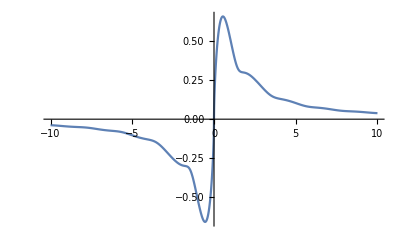

```mathematica
Plot[1/(1+x^2)*If[x≥0,(x^3+x^2*Sin[3x])^(1/5),-(-x^3-x^2*Sin[3x])^(1/5)],{x,-10,10}]
```

## Continuity of Arithmetic Combinations of Continuous Functions (including Polynomials and Rational Functions)

## Continuity of Trigonometric Functions

## Continuity of Composite Functions and Inverse Functions